```mathematica
ClearAll["Global`*"]
```

Value Declaration

## Value from Field tests

```mathematica
dist = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1};
prssi={-49,-82.5,-85,-88,-99,-99,-104,-99,-105,-105,-106,-105};
snr1 ={9,9,8,8,4,4,3,-1,-3,-5,-7,-9};
totPacket1 = {100/100,99/100,100/100,98/100,98/100,99/100,95/100,95/100,93/100,88/100,75/100,23/100};
```

## Values for Formulas

```mathematica
Subscript[h, b]=Subscript[h, m]=1;
f =868.1;
Subscript[Pt, W]=100*10^-3;
Subscript[Pt, dBm]=10*Log10[Subscript[Pt, W]]+30;
Subscript[Pt, dBw]=10*Log10[Subscript[Pt, W]];
Subscript[Gt, dBi]=Subscript[Gr, dBi]=3.43;
BW=125000;
x=43.5;
Subscript[L, 0]=89;
NF=6;
```

Formulas Declaration

## Field Test

```mathematica
rssi =Transpose[{dist,prssi}];
per=Transpose[{dist,totPacket1}];
snr = Transpose[{dist,snr1}];
paraSNR = Fit[snr,{1,kx,kx^2,kx^3,kx^4,kx^5},kx];
paraRSSI= Fit[rssi,{1,kx,kx^2,kx^3,kx^4,kx^5},kx];
paraPER= Fit[per,{1,1,kx,kx^2,kx^3,kx^4,kx^5,kx^6,kx^7,kx^8},kx];
```

## Hata Model Open Area

```mathematica
xa[h_]:=(1.1*Log10[f]-0.7)*h-(1.56*Log10[f]-0.8);
a=69.55+26.161*Log10[f]-13.82*Log10[Subscript[h, b]]-xa[Subscript[h, m]];
b=44.9-6.55*Log10[Subscript[h, b]];
c=40.94+4.78*(Log10[f])^2-18.33*Log10[f];
LHata[d_]:=a+b*Log10[d]-c;

Subscript[PrHata, dBm][d_]:=Subscript[Pt, dBm]+Subscript[Gt, dBi]+Subscript[Gr, dBi]-LHata[d];
Subscript[PrHata, dBw][d_]:=Subscript[Pt, dBw]+Subscript[Gt, dBi]+Subscript[Gr, dBi]-LHata[d];

intersection1Hata={d,-117.67}/.NSolve[Subscript[PrHata, dBm][d]==-117.6,d];
intersection2Hata={d,-148}/.NSolve[Subscript[PrHata, dBm][d]==-148,d];
```

## LEE Model

```mathematica
Subscript[F, 1][h_]:=(h/30.48)^2;
Subscript[F, 2][G_]:=G/4;
Subscript[F, 3][h_]:=(h/3);
Subscript[F, 4][f_,n_]:=(f/900)^-n;
Subscript[F, 5][G_]:=G/1;
Subscript[F, 0]=Subscript[F, 1][1]*Subscript[F, 2][Subscript[Gr, dBi]-2.15]*Subscript[F, 3][1]*Subscript[F, 4][868.1,2.5]*Subscript[F, 5][Subscript[Gt, dBi]-2.15];
LtotalLEE[d_]:=Subscript[L, 0]+x*Log10[d]-10*Log10[Subscript[F, 0]];
Subscript[PrLEE, dBm][d_]:=Subscript[Pt, dBm]+Subscript[Gt, dBi]+Subscript[Gr, dBi]-LtotalLEE[d];
Subscript[PrLEE, dBw][d_]:=Subscript[Pt, dBw]+Subscript[Gt, dBi]+Subscript[Gr, dBi]-LtotalLEE[d];
intersection1LEE={d,-117.67}/.NSolve[Subscript[PrLEE, dBm][d]==-117.6,d];
intersection2LEE={d,-148}/.NSolve[Subscript[PrLEE, dBm][d]==-148,d];
```

## Noise Signal

```mathematica
CG[SF_]:=2.5*SF;
Subscript[N, dBm][spreadFactor_]:=-174+NF+10*Log10[125000]+CG [spreadFactor];
```

Plot

## Propagation Loss

### Estimated

#### Hata Model Open Area

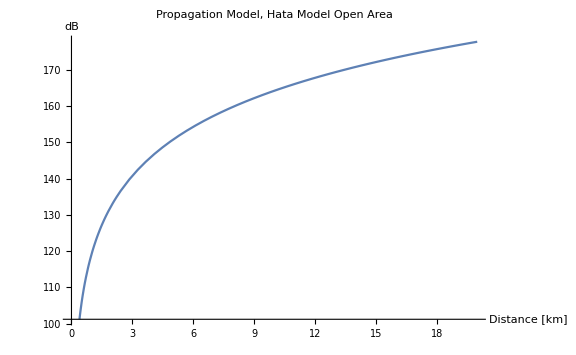

```mathematica
Plot[LHata[d],{d,0,20},AxesLabel->{"Distance [km]","dB"},PlotLabel->"Propagation Model, Hata Model Open Area",ImageSize->Large]
```

#### LEE Model

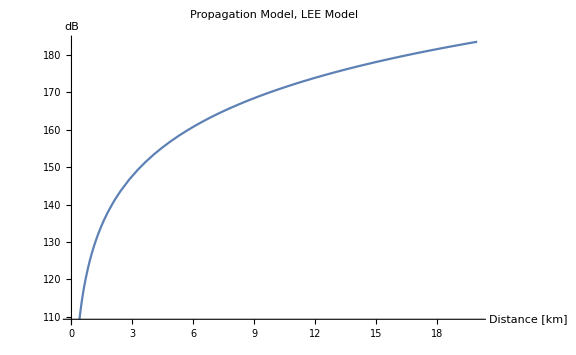

```mathematica
Plot[LtotalLEE[d],{d,0,20},AxesLabel->{"Distance [km]","dB"},ImageSize->Large,PlotLabel->"Propagation Model, LEE Model"]
```

## Received Signal Strength Indicator (RSSI)

### Estimated

#### Hata Model Open Area

```mathematica
Rasterize[Plot[{Subscript[PrHata, dBm][d],-117.67,-148},{d,0,20},AxesLabel->{"Distance [km]","RSSI [dBm]"},ImageSize->Large,Epilog->{PointSize[Large],Black,Point[intersection1Hata],Point[intersection2Hata]},PlotLabel-> "Recieved Signal Strength Indicator, Hata Model Open Area",PlotLegends->{"P_r(Recieved Power)","Spread Factor = 7", "Spread Factor = 12"}]
]
Rasterize[LogLinearPlot[{Subscript[PrHata, dBm][d],-117.67,-148},{d,0,20},AxesLabel->{"Distance [km]","dB"},ImageSize->Large,PlotLabel-> "Recieved Signal Power, Hata Model Open Area",PlotLegends->{"P_r(Recieved Power)","SF = 7", "SF = 12"}]
]
```

-Graphics-

-Graphics-

#### LEE Model

```mathematica
Rasterize[Plot[{Subscript[PrLEE, dBm][d],-117.67,-148},{d,0,17},AxesLabel->{"Distance [km]","RSSI [dBm]"},ImageSize->Large,Epilog->{PointSize[Large],Black,Point[intersection1LEE],Point[intersection2LEE]},PlotLabel-> "Recieved Signal Strength Indicator, LEE Model",PlotLegends->{"P_r(Recieved Power)","Spread Factor = 7", "Spread Factor = 12"}]]
Rasterize[LogLinearPlot[{Subscript[PrLEE, dBm][d],-117.67,-148},{d,0,17},AxesLabel->{"Distance [km]","dB"},
ImageSize->Large,PlotLabel-> "Recieved Signal Power, LEE Model",
PlotLegends->{"P_r(Recieved Power)","SF = 7", "SF = 12"}]]
```

-Graphics-

-Graphics-

### Measured

```mathematica
Rasterize[Show[
ListPlot[rssi],
Plot[paraRSSI,{kx,0,1.1},PlotStyle->{Dashed,RGBColor[0.27,0.49,1.]},PlotLegends->{"Approximated Function, Field Tests"}],
Plot[{Subscript[PrHata, dBm][d],-117.67,-148},{d,0,1.7},PlotStyle->RGBColor[1.,0.48,0.17],PlotLegends->{"RSSI Hata Model"}],
Plot[{Subscript[PrLEE, dBm][d],-117.67,-148},{d,0,1.7},PlotStyle->RGBColor[0.,0.56,0.26],PlotLegends->{"RSSI LEE Model"}],
Plot[-117.67,{d,0,1.7},PlotLegends->{"RSSI Limit, SF = 7"},PlotStyle->RGBColor[0.77,0.22,0.]],
Plot[-148,{d,0,1.7},PlotLegends->{"RSSI Limit, SF = 12"},PlotStyle->RGBColor[0.25,0.19,0.]],
PlotRange->Automatic,
ImageSize->Large,
AxesLabel->{"Distance [km]","RSSI [dBm]"},
PlotLabel-> "Recieved Signal Strength Indicator"
]
]
```

-Graphics-

## Signal-to-Noise Ratio (SNR)

### Estimated

#### Hata Model Open Area

```mathematica
SignalToNoise[SpreadFactor_,dist_] :=Subscript[PrHata, dBm][dist]-Subscript[N, dBm][SpreadFactor];
Rasterize[LogLinearPlot[{SignalToNoise[7,dist],SignalToNoise[12,dist],-7.5,-20},
{dist,0,10},
PlotLegends->{"SNR, Spread Factor = 7","SNR, Spread Factor = 12","SNR Demodulator, Spread Factor = 7","SNR Demodulator, Spread Factor = 12"},
ImageSize->Large,
PlotLabel->"SNR Estimation, Hata Model Open Area",
AxesLabel->{"Distance [km]","SNR [dB]"}
]
]
```

-Graphics-

#### LEE Model

```mathematica
SignalToNoise[SpreadFactor_,dist_] :=Subscript[PrLEE, dBm][dist]-Subscript[N, dBm][SpreadFactor];
Rasterize[LogLinearPlot[{SignalToNoise[7,dist],SignalToNoise[12,dist],-7.5,-20},
{dist,0,10},
PlotLegends->{"SNR, Spread Factor = 7","SNR, Spread Factor = 12","SNR Demodulator, Spread Factor = 7","SNR Demodulator, Spread Factor = 12"},
ImageSize->Large,
PlotLabel->"SNR Estimation, LEE Model",
AxesLabel->{"Distance [km]","SNR [dB]"}
]
]
```

-Graphics-

### Measured

```mathematica
Rasterize[Show[ListPlot[snr],
Plot[paraSNR,{kx,0,1.2},PlotLegends->{"Approximated Function, Field Tests"},PlotStyle->{Dashed,RGBColor[0.27,0.49,1.]}],
Plot[-7.5,{kx,0,1.5},PlotStyle->RGBColor[1.,0.48,0.17],PlotLegends->{"SNR Limit, SF = 7"}],
Plot[-20,{kx,0,1.5},PlotStyle->RGBColor[0.,0.56,0.26],PlotLegends->{"SNR Limit, SF = 12"}],
PlotLabel-> "Signal to Noise Ratio",
ImageSize->Large,
PlotRange->Automatic,
AxesLabel->{ "Distance [km]","SNR [dB]"}
]
]
```

-Graphics-

## Packet Error Rate (PER)

### Measured

```mathematica
Rasterize[Show[ListLogLinearPlot[per],
LogLinearPlot[paraPER,{kx,0,20},PlotLegends->{"Approximated Function, Field Tests"},PlotStyle->{Dashed,RGBColor[0.27,0.49,1.]}],
PlotLabel-> "Packet Error Rate, Field Tests",
AxesLabel-> {"Distance [km]","PER"},
ImageSize->Large
]
]
```

-Graphics-